```mathematica
collision=Import["/home/johann/Documents/Projects/transportEquations/collision_cpp/T_dependence.dat","Table"];
```

```mathematica
T=Table[100-i,{i,0,99}];
```

```mathematica
collisionT=Thread[{T,collision[[All,1]]}];
```

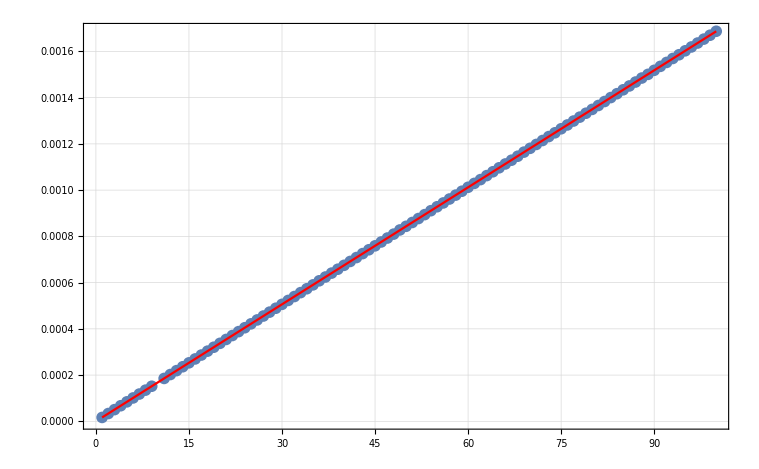

```mathematica
Show[ListPlot[{collisionT},PlotTheme->"FrameGrid",PlotRange->All,FrameStyle->Thick],Plot[0.000016868483437079084 x,{x,1,100},PlotStyle->Red]]
```

```mathematica
Fit[collisionT,{1,x},x]
```

-1.24305×10^-8+0.0000168685 x